# II Encryption

KTH/ICT:IX1500 - Discrete Mathematics
Göran Andersson, goeran@kth.se
rev. 170917

## Section. Implementation and Assessment

The course includes two-three project tasks on a total of 4 hp. The projects are assessed in writing and orally.  They will be given a summary grade in scale A-F. The assessment includes the number of solved project tasks and the quality. The first two projects are mandatory for grade E. The third project task is optional and targets higher grades A-D. In general, excellent performance increases the grade one step.

In this project task you will work in a group of two and solve a mathematical task, write a report (English) in Mathematica and prepare a short oral presentation on your solution to the task (English).

Carefully read the following information so that you know which rules apply and what is expected of you.

### Section.Subsection Report

The report should be written in Mathematica and contain

title and authors of the report

email@kth.se

a summary containing the results of resolved parts

separate sections for each part containing e.g.

mathematical formulas and equations

a brief discussion

explanatory diagrams

your conclusions.

separate code section (do not mix code and text with conclusions and results)

The report will normally be uploaded one-two days prior to the examination (see 1.5 below).

### Section.Subsection Oral Presentation

You should prepare an oral presentation of your solution to the task. The presentation will be carried out with your own laptop and should not take more than five minutes, effective time. A computer projector will be available at the presentation. Please carefully consider your presentation, what is important, in what order and how it will be illustrated. Practice the presentation in advance and make sure to meet the time frame. One of you in the group (of two) will be selected randomly for the oral presentation and the other part will be selected for questioning.

### Section.Subsection Rules

The task is considered individually and assumes that you have full knowledge of all the material you are presenting. In order to be approved, then you have solved the task and be able to explain the entire task and solution.

To account for the task that you do not have solved is considered cheating. It is also cheating to copy the solution or part of a solution from another. If two solutions are presented as (partially) copies they are rejected both.

If the solution contains parts, e.g. background material, which you do not have produced, you must clearly indicate this and indicate the source.

Suspicion of cheating or misleading can be reported to the Disciplinary Board.

### Section.Subsection Examination

The examination is carried out according to the booking in canvas 2017-10-05.

The booking is done according to information at KTH Social  Projektuppgifter/Projekt 2.

Please notice that this project should be reported in groups of two students.

The report (including code section) should be uploaded according to the information in Canvas.

A printed copy of the report must be submitted at examination. Don’t print the code section.

Notice that the report shall always be uploaded in time even if you cannot attend at the oral presentation. In case of illness, etc., then the oral presentation may be made during project 3. If you are unable to attend, you must in advance inform the teacher (in writing).

If you ignore the oral presentation or the uploading of the report without contacting the teacher (in writing) you will have to wait for the next course for a new project exam.

## Section. Preparations

### Section.Subsection Study

Read and study the following texts:

Chapter 4-6, especially example 35 pp. 167-68

lecture notes F8-F12

In this notebook most of the text and examples is mandatory (need to know). The notation ★ means nice to know; helpful but not necessary for the task, ★★ denotes higher grade level and ★★★ is used for supplementary study. A 💡 means important example; think about this.

### Section.Subsection Guidance

#### Section.Subsection.Subsubsection Caesar Cipher (★)

A very famous (and simple) encryption scheme is the Caesar cipher which is built on a cyclic alphabet shift (3 steps). Here’s an example using English block letters.

```mathematica
ClearAll["`*"]
```

```mathematica
shift=3;
```

```mathematica
alphabet=CharacterRange["A","Z"]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

```mathematica
substitution=RotateRight[alphabet,shift]
```

{X,Y,Z,A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W}

```mathematica
TableForm[{alphabet,substitution},TableSpacing->{1, 1}]
```

A | B | C | D | E | F | G | H | I | J | K | L | M | N | O | P | Q | R | S | T | U | V | W | X | Y | Z
X | Y | Z | A | B | C | D | E | F | G | H | I | J | K | L | M | N | O | P | Q | R | S | T | U | V | W

The substitutions for encryption and decryption are:

```mathematica
encrypt=Thread[alphabet->substitution]
```

{A→X,B→Y,C→Z,D→A,E→B,F→C,G→D,H→E,I→F,J→G,K→H,L→I,M→J,N→K,O→L,P→M,Q→N,R→O,S→P,T→Q,U→R,V→S,W→T,X→U,Y→V,Z→W}

```mathematica
decrypt=Thread[substitution->alphabet]
```

{X→A,Y→B,Z→C,A→D,B→E,C→F,D→G,E→H,F→I,G→J,H→K,I→L,J→M,K→N,L→O,M→P,N→Q,O→R,P→S,Q→T,R→U,S→V,T→W,U→X,V→Y,W→Z}

Now, the encryption goes:

```mathematica
message="SENDMOREMONEY";
```

```mathematica
cipher=StringReplace[message,encrypt]
```

PBKAJLOBJLKBV

The decryption is the other way around.

```mathematica
StringReplace[cipher,decrypt]
```

SENDMOREMONEY

This is of course insecure today and we need more sophisticated methods.

#### Section.Subsection.Subsubsection Hill Cipher (★)

A more complicated shift is provided by a shift matrix. Here’s an example that is using the 26 English block letters. We introduce a message matrix 𝕄, a key matrix 𝕂. We compute the operations mod 26. The encryption goes

ℂ≡_26 𝕂·𝕄

where ℂ is the cipher matrix. The decryption goes

𝕄≡_26 𝕂^-1·ℂ

The key matrix has to be invertible mod 26. This means that the determinant Abs[𝕂]∈ℤ_26 has to be invertible, i.e. gcd(Abs[𝕂],26)=1. The the inverse can be computed by

𝕂·𝕩=𝟙·𝕪⇔𝕂^-1·𝕂·𝕩=𝕂^-1·𝟙·𝕪⇔𝟙·𝕩=𝕂^-1·𝕪

∴(𝕂|𝟙)∼…∼(𝟙|𝕂^-1)

where the operations are performed mod 26 (see reduced row echelon form in linear algebra course).

Let’s pick a 3×3 key matrix for simplicity.

𝕂=(19 | 1 | 17
9 | 8 | 9
8 | 14 | 1)

We can easily find the determinant here.

|𝕂|=|19 | 1 | 17
9 | 8 | 9
8 | 14 | 1|=19|8 | 9
14 | 1|-1|9 | 9
8 | 1|+17|9 | 8
8 | 14|=19(-118)-(-63)+17 62=-1125≡_26 19

The Euclidean algorithm goes:

26=1×19+7, 19=3×7-2,7=3×2+1,2=2×1+0

Since 26 and 19 are co-primes (relatively prime) the inverse to 19 mod 26 can be found. This also mean that the inverse matrix exists mod 26. In order to find 𝕂^-1 mod 26 we start with the matrix (𝕂|𝟙) and find the row reduced Echelon form (𝟙|𝕂^-1). All operations are performed modulo 26.

(𝕂|𝟙)=(19 | 1 | 17 | 1 | 0 | 0
9 | 8 | 9 | 0 | 1 | 0
8 | 14 | 1 | 0 | 0 | 1)∼⟨r_1:=r_1-2 r_2⟩∼(1 | 11 | 25 | 1 | 24 | 0
9 | 8 | 9 | 0 | 1 | 0
8 | 14 | 1 | 0 | 0 | 1)

The first calculation is done as

r_1:=r_1-2 r_2=(19,1,17,1,0,0)-2(9,8,9,0,1,0)=(1,-15,-1,1,-2,0)≡_26(1,11,25,1,24,0)

Notice that our goal is to create the identity matrix to the left. We continue as

∼⟨r_2:=r_2-9 r_1,r_3:=r_3-8 r_1⟩∼(1 | 11 | 25 | 1 | 24 | 0
0 | 13 | 18 | 17 | 19 | 0
0 | 4 | 9 | 18 | 16 | 1)∼⟨r_2:=r_2-3 r_3⟩∼(1 | 11 | 25 | 1 | 24 | 0
9 | 8 | 9 | 15 | 23 | 23
8 | 14 | 1 | 18 | 16 | 1)

∼⟨r_3:=r_3-4 r_2⟩∼(1 | 11 | 25 | 1 | 24 | 0
0 | 1 | 17 | 15 | 23 | 23
0 | 0 | 19 | 10 | 2 | 13)∼⟨r_3:=19^-1 r_3≡_26 11 r_3⟩∼(1 | 11 | 25 | 1 | 24 | 0
0 | 1 | 17 | 15 | 23 | 23
0 | 0 | 1 | 6 | 22 | 13)

∼⟨r_1:=r_1+r_3,r_2:=r_2+9 r_3⟩∼(1 | 11 | 0 | 7 | 20 | 13
0 | 1 | 0 | 17 | 13 | 10
0 | 0 | 1 | 6 | 22 | 13)∼⟨r_1:=r_1-11 r_2⟩∼(1 | 0 | 0 | 2 | 7 | 7
0 | 1 | 0 | 17 | 13 | 10
0 | 0 | 1 | 6 | 22 | 13)=(𝟙|𝕂^-1)

∴𝕂^-1≡_26(2 | 7 | 7
17 | 13 | 10
6 | 22 | 13)

The message “DISCRETEMATHEMATICS” is divided into columns of length three, appended with Z and converted into numbers in ℤ_26.

𝕄=(3 | 2 | 19 | 0 | 4 | 19 | 18
8 | 17 | 4 | 19 | 12 | 8 | 25
18 | 4 | 12 | 7 | 0 | 2 | 25)

The cipher matrix is simply computed by

ℂ=𝕂·𝕄=(19 | 1 | 17
9 | 8 | 9
8 | 14 | 1)·(3 | 2 | 19 | 0 | 4 | 19 | 18
8 | 17 | 4 | 19 | 12 | 8 | 25
18 | 4 | 12 | 7 | 0 | 2 | 25)≡_26(7 | 19 | 23 | 8 | 10 | 13 | 12
19 | 8 | 25 | 7 | 2 | 19 | 15
24 | 24 | 12 | 13 | 18 | 6 | 25)

So the cipher is then “HTYTIYXZMIHNKCSNTGMPZ”.

The decryption goes as

𝕄=𝕂^-1·ℂ=(2 | 7 | 7
17 | 13 | 10
6 | 22 | 13)·(7 | 19 | 23 | 8 | 10 | 13 | 12
19 | 8 | 25 | 7 | 2 | 19 | 15
24 | 24 | 12 | 13 | 18 | 6 | 25)≡_26(3 | 2 | 19 | 0 | 4 | 19 | 18
8 | 17 | 4 | 19 | 12 | 8 | 25
18 | 4 | 12 | 7 | 0 | 2 | 25)

which corresponds to “DISCRETEMATHEMATICSZZ”.

Mathematica. We pick a slightly larger example, since we have computer support. The key is chosen to be a 5×5 matrix. This means that the column length should be 5 in the message matrix.

```mathematica
ClearAll["`*"]
```

We transform the message into ℤ_26.

```mathematica
m=26; A=65;
message="THISISASECRETTHATCANNOTBEREVEALEDFORANYONEBUTYOU";
message26=ToCharacterCode[message]-A
```

{19,7,8,18,8,18,0,18,4,2,17,4,19,19,7,0,19,2,0,13,13,14,19,1,4,17,4,21,4,0,11,4,3,5,14,17,0,13,24,14,13,4,1,20,19,24,14,20}

```mathematica
n=5; (* column length *)
```

```mathematica
pad=ToCharacterCode["Z"]⟦1⟧-A
```

25

```mathematica
𝕄=Transpose@Partition[
Mod[message26,m],
n,n,1,pad];
MatrixForm[𝕄]
```

(19 | 18 | 17 | 0 | 13 | 17 | 11 | 17 | 13 | 24
7 | 0 | 4 | 19 | 14 | 4 | 4 | 0 | 4 | 14
8 | 18 | 19 | 2 | 19 | 21 | 3 | 13 | 1 | 20
18 | 4 | 19 | 0 | 1 | 4 | 5 | 24 | 20 | 25
8 | 2 | 7 | 13 | 4 | 0 | 14 | 14 | 19 | 25)

Next, we create an invertible matrix,

```mathematica
𝕂=RandomInteger[{0,m-1},{n,n}];
While[GCD[Det[𝕂],m]≠1,
𝕂=RandomInteger[{0,m-1},{n,n}];
];
MatrixForm[𝕂]
```

(8 | 14 | 2 | 7 | 21
15 | 20 | 13 | 0 | 8
13 | 1 | 17 | 1 | 9
17 | 10 | 8 | 7 | 20
16 | 24 | 24 | 20 | 13)

```mathematica
MatrixForm[
𝕂1=Inverse[𝕂,Modulus->m]
]
```

(19 | 16 | 22 | 19 | 9
9 | 25 | 23 | 4 | 6
21 | 3 | 0 | 19 | 25
19 | 16 | 12 | 4 | 7
2 | 10 | 2 | 8 | 25)

Now, the encryption goes:

```mathematica
MatrixForm[
ℂ=Mod[𝕂.𝕄,m]
]
```

(14 | 16 | 16 | 23 | 13 | 2 | 11 | 0 | 25 | 10
21 | 0 | 14 | 16 | 0 | 10 | 6 | 16 | 24 | 8
12 | 16 | 6 | 14 | 23 | 14 | 17 | 20 | 17 | 6
15 | 24 | 0 | 24 | 2 | 5 | 20 | 9 | 9 | 5
10 | 20 | 21 | 23 | 6 | 16 | 2 | 24 | 13 | 23)

```mathematica
cipher=FromCharacterCode[Flatten[Transpose[ℂ]]+A]
```

OVMPKQAQYUQOGAVXQOYXNAXCGCKOFQLGRUCAQUJYZYRJNKIGFX

The decryption use the inverse key 𝕂^-1.

```mathematica
ℂr=Transpose@Partition[
ToCharacterCode[cipher]-A,
n];
MatrixForm[ℂr]
```

(14 | 16 | 16 | 23 | 13 | 2 | 11 | 0 | 25 | 10
21 | 0 | 14 | 16 | 0 | 10 | 6 | 16 | 24 | 8
12 | 16 | 6 | 14 | 23 | 14 | 17 | 20 | 17 | 6
15 | 24 | 0 | 24 | 2 | 5 | 20 | 9 | 9 | 5
10 | 20 | 21 | 23 | 6 | 16 | 2 | 24 | 13 | 23)

```mathematica
MatrixForm[
𝕄r=Mod[𝕂1.ℂr,m]
]
```

(19 | 18 | 17 | 0 | 13 | 17 | 11 | 17 | 13 | 24
7 | 0 | 4 | 19 | 14 | 4 | 4 | 0 | 4 | 14
8 | 18 | 19 | 2 | 19 | 21 | 3 | 13 | 1 | 20
18 | 4 | 19 | 0 | 1 | 4 | 5 | 24 | 20 | 25
8 | 2 | 7 | 13 | 4 | 0 | 14 | 14 | 19 | 25)

```mathematica
receivedmessage=FromCharacterCode[Flatten@Transpose[𝕄r]+A]
```

THISISASECRETTHATCANNOTBEREVEALEDFORANYONEBUTYOUZZ

The Hill Cipher (1929) is of course also out of date and we need more sophisticated methods.

#### Section.Subsection.Subsubsection Euler’s Totient Theorem

According to Fermat’s Little Theorem we know that a^(p-1)=1 in the field ℤ_p. Euler did extend this result to the ring ℤ_n.

a∈ℤ_n,(a,n)=1⇒a^n≡_n 1

n can also be denoted by curly phi φ(n).

In order to prove the theorem we can notice that for if a and x_i are invertible then x_i→a x_i is a bijection. Now, if x_1,…,x_n are all invertible elements then a x_1,…,a x_n is a permutation mod n, i.e. with the same product.

∏_(i=1)^(ϕ(n)) (a x_i)≡_n∏_(i=1)^(ϕ(n)) x_i⇔a^(ϕ(n))∏_(i=1)^(ϕ(n)) x_i≡_n∏_(i=1)^(ϕ(n)) x_i⇔a^(ϕ(n))≡_n 1

Example

What is 14^792002 mod 1356531 ?

Solution:

a=14=2 7,n=1356531=3 11^2 37 101⇒(a,n)=1

1356531=3 11^2 37 101× (1-1/3)(1-1/11)(1-1/37)(1-1/101)=11 2 10 36 100=792000

Euler’s Totient Theorem gives

14^792002=14^(φ(n)+2)≡_n 14^2=196

Mathematica

```mathematica
PowerMod[14,792002,1356531]
```

196

#### Section.Subsection.Subsubsection RSA

RSA encryption, which is an asymmetric method, was described 1977 by Ron Rivest, Adi Shamir and Len Adleman. The method take advantage of Euler’s Totient Theorem. Its security is built on that it is time consuming to factor numbers with large prime factors only.

Consider the following example about the time to factor two consecutive (not too) large integers.

```mathematica
n=38! (* easy to factor *)
```

523022617466601111760007224100074291200000000

```mathematica
{t1,f1}=AbsoluteTiming[FactorInteger[n]]
```

{0.0000339492,{{2,35},{3,17},{5,8},{7,5},{11,3},{13,2},{17,2},{19,2},{23,1},{29,1},{31,1},{37,1}}}

```mathematica
{t2,f1}=AbsoluteTiming[FactorInteger[n+1]]
```

{0.352711,{{14029308060317546154181,1},{37280713718589679646221,1}}}

```mathematica
t2/t1
```

10389.4

We can see that the second number 38!+1 takes many times longer to factor than 38!.

Let’s say Alice and Bob want to exchange messages. They both follow the steps 1,2,3 and 4 below.

Choose two large prime numbers p,q (size ≳2^2024 or even 2^4096) and build n=p q.

Now, choose an encryption key e (size a few digits) which is relatively prime to ϕ=(p-1)(q-1).

Finally, determine an inverse d to e in the ring ℤ_ϕ, d e≡_ϕ 1. The inverse d is the decryption key.

Publish (n,e) with an encryption description, but keep (d,p,q) secret.

Let’s say Alice wants to send a message to Bob.

m_Alice<n_Bob

c_Alice≡_n_Bob m_Alice^e_Bob

Bob decrypts the cipher by

m_Alice≡_n_Bob c_Alice^d_Bob

Explanation:

Since d is the inverse to e in the ring ℤ_ϕ there is an integer k (Bézout’s Identity) so that

e d≡_ϕ 1⇔e d=1+k ϕ

i.e. using Euler’s Totient Theorem (*)

c^d=m^(e d)=m^(1+k ϕ)=m (m^ϕ)^k(≡_n)^(*)m (1)^k≡_n m

That is the clear text is revealed by computing c^d mod(n).

Notice that you have to have a message m<n in order to avoid ambiguity.

RSA is usually only used in the beginning of an encryption session in order to transfer a key for a symmetric encryption method, e.g. for advanced encryption standard (AES). The reason is that a symmetric method is in general faster.

Mathematica

Once again let’s say Alice wants to send a message to Bob. We create primes (small scale trial with 15-20 figures) och and key according to the description above.

```mathematica
ClearAll["`*"]
```

```mathematica
pBob=NextPrime[RandomInteger[{10^15,10^20}]]
```

61719681874419997579

```mathematica
qBob=NextPrime[RandomInteger[{10^15,10^20}]]
```

45087105771035274937

```mathematica
nBob=pBob qBob
```

2782761824826623128011717135735139377523

```mathematica
ϕBob=(pBob-1)(qBob-1)
```

2782761824826623127904910348089684105008

```mathematica
rnd:=RandomInteger[{10^3,10^4}]
```

```mathematica
While[GCD[eBob=rnd,ϕBob]≠1];
eBob
```

6469

```mathematica
dBob=PowerMod[eBob,-1,ϕBob]
```

2075564353808696335158632312495397404029

```mathematica
messageAlice="discrete math";
```

```mathematica
ascii=ToCharacterCode[messageAlice]
```

{100,105,115,99,114,101,116,101,32,109,97,116,104}

Now we create a message as a single number m_Alice<n_Bob by coding the ascii numbers in a position system with the base 256 (or another suitable base).

```mathematica
B=256;
B^(Range[StringLength[messageAlice]]-1)
```

{1,256,65536,16777216,4294967296,1099511627776,281474976710656,72057594037927936,18446744073709551616,4722366482869645213696,1208925819614629174706176,309485009821345068724781056,79228162514264337593543950336}

We take advantage of the scalar product to create the message c_0 B^0+c_1 B^1+c_2 B^2+…

```mathematica
mAlice=ToCharacterCode[messageAlice]. B^(Range[StringLength[messageAlice]]-1)
```

8275746943762822779517724223844

The encryption is done by Alice:

```mathematica
cAlice=PowerMod[mAlice,eBob,nBob]
```

325230066098595166519846113430798858843

The cipher c_Alice is sent to Bob. The decryption is done by Bob:

```mathematica
mFromAlice=PowerMod[cAlice,dBob,nBob]
```

8275746943762822779517724223844

This number contains the message text which is revealed by extracting the ascii characters one by one module B.

```mathematica
firstcharacter=Mod[mFromAlice,B]
```

100

Here’s a loop fir the rest.

```mathematica
q=mFromAlice;ascii={};
While[q≠0,
AppendTo[ascii,Mod[q,B]];
q=Quotient[q,B]
];
ascii
```

{100,105,115,99,114,101,116,101,32,109,97,116,104}

```mathematica
messageFromAlice=FromCharacterCode[ascii]
```

discrete math

#### Section.Subsection.Subsubsection About Primes

Large primes (>1000bits) are usually created by statistical methods. According to Gauss’ prime-counting function π(n) the number of primes less or equal than n is approximately

π(n)≈n/(ln(n))

At the end of the 19^th century it was proved that the error approach 0 as n→∞. We can use this formula to estimate the probability of hitting a prime in with an odd random number in [n/2,n)=[2^b,2^(b+1)), where n consists of b bits.

p=(#primes)/(#odd numbers)=(π(n)-π(n/2))/(1/2(n-n/2))≈2(n/ln(n)-(n/2)/ln(n/2))/(n-n/2)=2/(b ln(2))((b-1)/(b+1))

If we try k times the probability not hitting a prime is (1-p)^k. Then the probability of hitting at least one prime is p_k=1-(1-p)^k. Now let’s make k=b and comparing with lim_(x→∞) (1+a/x)^x=e^a we get

p_b=1-(1-2/(b ln(2))((b-1)/(b+1)))^b→1-e^(-2/ln(2))≈0.944

so if we try b=100 times for a 100-bits prime we have 94% probability of hitting at least one prime. If we try 3b times the probability is 1-e^(-3×2/ln(2))≈0.9998. Now, the found prime candidates are tested statistically. The probability of that the number is composite decreases fast with the number of tested factors.

In Mathematica the correct x,x≲10^15  can be computed with PrimePi.

```mathematica
PrimePi[25]
```

9

```mathematica
PrimePi[10^6]
```

78498

Let’s generate 250 odd numbers with 250 bits and extract a prime number. A well-know method is the  which tests a number and responds true with an error of 4^-k.

```mathematica
nlist=2RandomInteger[{2^248,2^249},250]-1;
Short[nlist,5]
```

{1013834771353362661565036878107606317744092843345581976241901010222200968763,1462905734084479195775582961215899285344630676027935912921901921162555806883,«246»,1063583175470660787912720749241908357556781906371643234717005426466537745211,1325386322851713454168047402221696535939086726933549133054190174717248412271}

Here's a code that implements the primal test. The parameter k is a quality parameter.
If you Compile the method (e.g. for C) you have to deal with machine size integers, typically in the range ±(2^63-1). However, larger integers can be handled by the Chinese remainder theorem (see Böiers, example 44, ch. 6.6).

```mathematica
MillerRabin[k_][n_]:=Module[
{d=n-1,r=0,a,x,i,result=True},
While[Mod[d,2]==0,d/=2;r++]; 
Do[
a=RandomInteger[{2,n-2}];
x=PowerMod[a,d,n];
If[x≠1,
For[i=0,i<r,i++,
If[x==n-1,Continue[]];
x=Mod[x x,n]
];
If[x≠n-1,result=False]
],
{k}
];
result
]
```

```mathematica
(* simple test *)
{MillerRabin[5][1001],MillerRabin[5][1009]}
```

{False,True}

```mathematica
(* the 250 bits number *)
plist=Select[nlist,MillerRabin[20]]
```

{955649205394886669813601392292531659265857470710834273135721574024067606619,1649549867999046118940990821257934258752591116139792895022462465359750571381,906993712129560527382419327463456435180606825902238232880040263431681844429,1641741645389828989718856323825089922236160190291271521600218294702650469893,1315206155828602315160019743479641951051466941464627393933478699649598251259,1501607162452997610321211905189075266027331856328925396084277760653588830103}

```mathematica
(* compare with built-in PrimeQ *)
Select[nlist,PrimeQ]
```

{955649205394886669813601392292531659265857470710834273135721574024067606619,1649549867999046118940990821257934258752591116139792895022462465359750571381,906993712129560527382419327463456435180606825902238232880040263431681844429,1641741645389828989718856323825089922236160190291271521600218294702650469893,1315206155828602315160019743479641951051466941464627393933478699649598251259,1501607162452997610321211905189075266027331856328925396084277760653588830103}

#### Section.Subsection.Subsubsection Using RSA for Authentication

In RSA it’s not just Alice that can send a message to Bob. Anyone that access Bob’s public keys can sen an encrypted message. So how can Bob know that the message is from Alice?

A rather straight forward way of doing this is that Alice also encrypt the message with her secret key d_Alice. Bob will later decrypt, using Alice’s public key.

Let’s say Alice wants to send a message to Bob.

m_Alice<min(n_Alice,n_Bob)

start with the key that belongs to min(n_Alice,n_Bob)

n_Alice<n_Bob⇒c_0≡_n_Alice m_Alice^d_Alice, c_Alice≡_n_Bob c_0^e_Bob

n_Bob<n_Alice⇒c_0≡_n_Bob m_Alice^e_Bob, c_Alice≡_n_Alice c_0^d_Alice

Bob decrypts the cipher by

start with the key that belongs to max(n_Alice,n_Bob)

n_Bob>n_Alice⇒c_1≡_n_Bob c_Alice^d_Bob, m_Alice≡_n_Alice c_1^e_Alice

n_Alice>n_Bob⇒c_1≡_n_Alice c_Alice^e_Alice, m_Alice≡_n_Bob c_1^d_Bob

Usually the authentication is not done on the full message, but rather a message digest or a cryptographic checksum, e.g. secure hash algorithm (SHA).

#### Section.Subsection.Subsubsection Diffie-Hellman Key Exchange (★)

This key exchange algorithm was published by Whitfield Diffie and Martin Hellman 1976. The algorithm shows how to exchange a secret key (e.g. for a symmetric encryption algorithm.

Public keys: Alice and Bob agree on a large prime p and a generator g for ℤ_p.

Alice picks a random number x in ℤ_p and computes X≡_p g^x. She sends X to Bob.

Bob picks a random number y in ℤ_p and computes Y≡_p g^y. He sends Y to Alice.

Alice computes K_A≡_p Y^x

Bob computes K_B≡_p X^y

Now Alice and Bob have the same key. Notice that this exchange method is sensible for a man-in-the-middle attack (since Bob is not authenticated).

Explanation:

K_A≡_p Y^x≡_p(g^y)^x≡_p(g^x)^y≡_p X^y≡_p K_B

Mathematica

Example with not too large numbers.

```mathematica
ClearAll["`*"]
```

```mathematica
p=NextPrime[RandomInteger[10^25]]
```

9838796690519166711385531

```mathematica
g=PrimitiveRoot[p,1000]
```

1001

```mathematica
x=RandomInteger[{2,p-1}]
```

8892297506483207455561732

```mathematica
X=PowerMod[g,x,p]
```

5341078167045592352845432

```mathematica
y=RandomInteger[{2,p-1}]
```

6568226080382210870863911

```mathematica
Y=PowerMod[g,y,p]
```

809429903214152086136943

```mathematica
KA=PowerMod[Y,x,p]
```

131297231884500199678843

```mathematica
KB=PowerMod[X,y,p]
```

131297231884500199678843

```mathematica
KA==KB
```

True

#### Section.Subsection.Subsubsection RSA in Mathematica (★★★)

Here’s the previous encryption (without Alice’s authentication) with built-in commands. We will now use professional number sizes.

```mathematica
ClearAll["`*"]
```

In this example we RSA (default) and 2048 bits (default) as a public modulus (n), which is the minimum recommended key size today. The public exponent (e) is by default the prime number 65537=2^16+1.

GenerateAsymmetricKeyPair[Method -> Association["Cipher" -> "RSA", "KeySize" -> 2048, "PublicExponent" -> 65537]]

The keys for Bob are:

```mathematica
keysBobRSA=GenerateAsymmetricKeyPair[]
```

<|PrivateKey→PrivateKey[…],PublicKey→PublicKey[…]|>

```mathematica
publicKeyBob=keysBobRSA["PublicKey"]
```

PublicKey[…]

```mathematica
privateKeyBob=keysBobRSA["PrivateKey"]
```

PrivateKey[…]

Now, Alice get the public keys for Bob and encrypt her message.

```mathematica
messageAlice="discrete math";
```

```mathematica
cipherObjectAliceRSA=Encrypt[publicKeyBob,messageAlice]
```

EncryptedObject[<|Data -> ByteArray[<256>], OriginalForm -> String|>]

Now, Bob decrypt using his private key.

```mathematica
Decrypt[privateKeyBob,cipherObjectAliceRSA]
```

discrete math

In order to exchange information outside Mathematica we need to use a standard formats.

```mathematica
Normal[publicKeyBob]
```

PublicKey[{Cipher→RSA,Padding→PKCS1,PublicExponent→65537,PublicModulus→23320313250164347135959708787789707735699570826934912893988317366684399599278479833407698827712400034312005461101541507673486455305660365538714628659570809377882166572188152982741107541247830049128517856423719784295933453823898091543415634341526473198738613588018138507745884987352168357368402806209897183637160677776108551956072220065428792524838973217748374329515228430876042224430198263689562231904506026246395814757616161963982818656550412284689824245225925043977301863515940069803030618670421931139508912779555767938631621882497275039015799371882901110470818936726155675160556700167960659614205773259438352555463}]

```mathematica
eBob=publicKeyBob["PublicExponent"]
```

65537

```mathematica
nBob=publicKeyBob["PublicModulus"]
```

23320313250164347135959708787789707735699570826934912893988317366684399599278479833407698827712400034312005461101541507673486455305660365538714628659570809377882166572188152982741107541247830049128517856423719784295933453823898091543415634341526473198738613588018138507745884987352168357368402806209897183637160677776108551956072220065428792524838973217748374329515228430876042224430198263689562231904506026246395814757616161963982818656550412284689824245225925043977301863515940069803030618670421931139508912779555767938631621882497275039015799371882901110470818936726155675160556700167960659614205773259438352555463

Alice creates a file with the encrypted bytes.

```mathematica
cipherBytesAliceRSA=Normal[cipherObjectAliceRSA["Data"]]
```

{141,236,227,206,45,191,51,145,79,38,102,44,174,8,250,38,245,235,102,101,199,62,149,6,243,76,113,165,174,76,126,139,32,204,204,236,76,69,151,195,248,209,251,124,222,57,97,238,0,188,214,56,16,211,231,22,112,152,242,23,232,213,155,223,61,35,192,223,40,15,59,175,12,247,121,246,178,121,248,62,112,65,84,10,80,242,160,9,102,58,253,217,174,225,8,63,75,222,206,67,184,127,149,149,215,211,172,153,97,57,82,195,12,123,185,108,228,222,132,230,214,87,67,75,133,71,106,48,218,132,99,76,71,146,236,4,168,132,147,36,39,46,12,10,251,85,15,57,21,193,229,237,74,0,199,169,55,138,234,214,131,90,48,250,208,151,29,30,172,163,224,95,142,172,240,135,130,138,30,95,197,245,3,254,143,255,154,104,40,98,255,217,8,251,57,154,108,98,105,252,222,60,197,11,135,16,122,11,151,217,151,121,15,116,77,22,9,15,176,164,148,230,165,107,201,26,255,247,95,105,68,12,255,86,165,57,194,0,7,59,61,99,249,67,24,148,127,98,47,68,167,156,145,17,27,216}

```mathematica
file=FileNameJoin[{NotebookDirectory[],"Alice.bin"}]
```

C:\Users\Evan\Downloads\Alice.bin

```mathematica
BinaryWrite[file,cipherBytesAliceRSA];Close[file]
```

C:\Users\Evan\Downloads\Alice.bin

Now, Bob reads the file from Alice and decrypts its contents.

```mathematica
cipherBytesFromAliceRSA=BinaryReadList[file]
```

{141,236,227,206,45,191,51,145,79,38,102,44,174,8,250,38,245,235,102,101,199,62,149,6,243,76,113,165,174,76,126,139,32,204,204,236,76,69,151,195,248,209,251,124,222,57,97,238,0,188,214,56,16,211,231,22,112,152,242,23,232,213,155,223,61,35,192,223,40,15,59,175,12,247,121,246,178,121,248,62,112,65,84,10,80,242,160,9,102,58,253,217,174,225,8,63,75,222,206,67,184,127,149,149,215,211,172,153,97,57,82,195,12,123,185,108,228,222,132,230,214,87,67,75,133,71,106,48,218,132,99,76,71,146,236,4,168,132,147,36,39,46,12,10,251,85,15,57,21,193,229,237,74,0,199,169,55,138,234,214,131,90,48,250,208,151,29,30,172,163,224,95,142,172,240,135,130,138,30,95,197,245,3,254,143,255,154,104,40,98,255,217,8,251,57,154,108,98,105,252,222,60,197,11,135,16,122,11,151,217,151,121,15,116,77,22,9,15,176,164,148,230,165,107,201,26,255,247,95,105,68,12,255,86,165,57,194,0,7,59,61,99,249,67,24,148,127,98,47,68,167,156,145,17,27,216}

```mathematica
object=EncryptedObject[Association["Data"->ByteArray[cipherBytesFromAliceRSA],"OriginalForm"->String]]
```

EncryptedObject[<|Data -> ByteArray[<256>], OriginalForm -> String|>]

The decryption goes

```mathematica
Decrypt[privateKeyBob,object]
```

discrete math

Instead of a binary file we can use a string format, e.g. Base64. This is easy to include in a text message. The InputForm of a byte array reveals the string.

```mathematica
InputForm[cipherObjectAliceRSA["Data"]]//StandardForm
```

ByteArray["jezjzi2/M5FPJmYsrgj6JvXrZmXHPpUG80xxpa5MfosgzMzsTEWXw/jR+3zeOWHuALzWOBDT5xZwmPIX6NWb3z0jwN8oDzuvDPd59rJ5+D5wQVQKUPKgCWY6/dmu4Qg/S97OQ7h/lZXX06yZYTlSwwx7uWzk3oTm1ldDS4VHajDahGNMR5LsBKiEkyQnLgwK+1UPORXB5e1KAMepN4rq1oNaMPrQlx0erKPgX46s8IeCih5fxfUD/o//mmgoYv/ZCPs5mmxiafzePMULhxB6C5fZl3kPdE0WCQ+wpJTmpWvJGv/3X2lEDP9WpTnCAAc7PWP5QxiUf2IvRKeckREb2A=="]

```mathematica
extractString[a_ByteArray]:=Module[
{str,s,e},
str=ToString[InputForm[a]];
{{s,s},{e,e}}=StringPosition[str,"\""];
StringTake[str,{s+1,e-1}]
]
```

```mathematica
cipherStringAliceRSA=extractString[cipherObjectAliceRSA["Data"]]
```

jezjzi2/M5FPJmYsrgj6JvXrZmXHPpUG80xxpa5MfosgzMzsTEWXw/jR+3zeOWHuALzWOBDT5xZwmPIX6NWb3z0jwN8oDzuvDPd59rJ5+D5wQVQKUPKgCWY6/dmu4Qg/S97OQ7h/lZXX06yZYTlSwwx7uWzk3oTm1ldDS4VHajDahGNMR5LsBKiEkyQnLgwK+1UPORXB5e1KAMepN4rq1oNaMPrQlx0erKPgX46s8IeCih5fxfUD/o//mmgoYv/ZCPs5mmxiafzePMULhxB6C5fZl3kPdE0WCQ+wpJTmpWvJGv/3X2lEDP9WpTnCAAc7PWP5QxiUf2IvRKeckREb2A==

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Evan\Downloads

```mathematica
Export["Alice.txt",cipherStringAliceRSA]
```

Alice.txt

```mathematica
cipherString=Import["Alice.txt"]
```

jezjzi2/M5FPJmYsrgj6JvXrZmXHPpUG80xxpa5MfosgzMzsTEWXw/jR+3zeOWHuALzWOBDT5xZwmPIX6NWb3z0jwN8oDzuvDPd59rJ5+D5wQVQKUPKgCWY6/dmu4Qg/S97OQ7h/lZXX06yZYTlSwwx7uWzk3oTm1ldDS4VHajDahGNMR5LsBKiEkyQnLgwK+1UPORXB5e1KAMepN4rq1oNaMPrQlx0erKPgX46s8IeCih5fxfUD/o//mmgoYv/ZCPs5mmxiafzePMULhxB6C5fZl3kPdE0WCQ+wpJTmpWvJGv/3X2lEDP9WpTnCAAc7PWP5QxiUf2IvRKeckREb2A==

```mathematica
object=EncryptedObject[Association["Data"->ByteArray[cipherString],"OriginalForm"->String]]
```

EncryptedObject[<|Data -> ByteArray[<256>], OriginalForm -> String|>]

```mathematica
Decrypt[privateKeyBob,object]
```

discrete math

#### Section.Subsection.Subsubsection A Complete File Example (★★★)

In this example we use a professional approach. Assume that Alice wants to transfer a file to Bob. In order to do that we want to use the symmetric encryption method AES256. The symmetric key is transferred to Bob with RSA4096. Alice also computes a cryptographic checksum with SHA512 for to secure the file and for authentication.

Encryption by Alice

Alice use the message file m_0 to compute a digest h_0=h(m_0) using SHA512. This is used to secure the file contents from modification.

Alice encrypts the digest with her private or secret decryption key d_A and get h_A=d_A(h_0). This is done to authenticate Alice.

Alice generates a symmetric key k_0 and initialization vector v_0 for AES256.

Alice encrypts the file and ends up with c_A=k_0(m_0).

Alice encrypts the key {k_0,v_0} with Bob’s public encryption key e_B and ends up with k_A=e_B({k_0,v_0}).

Finally, the information {h_A,k_A,c_A} is transferred to Bob.

After receiving the information the next phase takes place:

Decryption by Bob

Bob use his private key to decrypt the file symmetric key k_1=d_B(k_A).

Bob decrypts the file by m_1=k_1(c_A).

Bob computes a digest using SHA512, h_1=h(m_1).

Bob decrypts the received digest with Alice’s public key by h_2=e_A(h_A).

If h_2=h_1 the file is accepted.

Mathematica

```mathematica
ClearAll["`*"]
```

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

C:\Users\Evan\Downloads

##### 0. Alice

Alice creates her RSA keys.

```mathematica
keysAlice=GenerateAsymmetricKeyPair[Method -> Association["Cipher" -> "RSA", "KeySize" -> 4096, "PublicExponent" -> 65537]];
eA=keysAlice["PublicKey"];
dA=keysAlice["PrivateKey"];
```

##### 0. Bob

Bob creates his RSA keys.

```mathematica
keysBob=GenerateAsymmetricKeyPair[Method -> Association["Cipher" -> "RSA", "KeySize" -> 4096, "PublicExponent" -> 65537]];
eB=keysBob["PublicKey"];
dB=keysBob["PrivateKey"];
```

##### 1. Alice

Alice save the clear text and computes a digest.

```mathematica
m0=WikipediaData["Moon"];
StringLength[m0]
```

59608

```mathematica
StringTake[m0,{1,250}] (* view part of the message *)
```

The Moon is an astronomical body that orbits planet Earth, being Earth's only permanent natural satellite. It is the fifth-largest natural satellite in the Solar System, and the largest among planetary satellites relative to the size of the planet th

```mathematica
Export["cleartext.txt",m0];
h0=FileHash["cleartext.txt", "SHA512"]
```

7094592555721684112707669445830371010973861453941727304357101405031146579795695924267610501791516156338051436450785843277869633560088162976628148600188571

##### 2. Alice

Alice encrypts the digest with her private key.

```mathematica
object=Encrypt[dA,h0];
hABytes=Normal[object["Data"]];
Length[hABytes]
```

512

##### 3. Alice

Alice generates a symmetric key. Notice that the mode of operation is CBC by default.

```mathematica
v0=RandomInteger[255,16]
```

{93,70,124,250,44,201,233,116,227,49,207,141,160,14,245,223}

```mathematica
k0=GenerateSymmetricKey[Method->Association["Cipher"->"AES256","InitializationVector"->ByteArray[v0]]]
```

SymmetricKey[…]

##### 4. Alice

Alice encrypts the message.

```mathematica
object=Encrypt[k0,m0];
cABytes=Normal[object["Data"]];
Short[cABytes]
```

{171,139,124,163,94,44,64,198,253,223,«59740»,242,191,126,170,211,253,183,92,217,116}

##### 5. Alice

Alice encrypts the symmetric key and the initialization vector.

```mathematica
object=Encrypt[eB,ByteArray[Join[Normal[k0["Key"]],v0]]];
kABytes=Normal[object["Data"]];
Length[kABytes]
```

512

##### 6. Alice

Save the file:

```mathematica
file=FileNameJoin[{dir,"Alice.bin"}];
stream=OpenWrite[file,BinaryFormat->True];
BinaryWrite[stream,hABytes];
BinaryWrite[stream,kABytes];
BinaryWrite[stream,cABytes];
Close[stream];
```

```mathematica
Clear[m0,h0,hABytes,kABytes,cABytes,object]
```

##### 7. Bob

Bob reads the file content, identify the symmetric key and decrypts it with his secret key.

```mathematica
block=512; (* bytes *)
file=FileNameJoin[{dir,"Alice.bin"}];
stream=OpenRead[file,BinaryFormat->True];
hABytes=BinaryReadList[stream,"Byte",block];
kABytes=BinaryReadList[stream,"Byte",block];
cABytes=BinaryReadList[stream];
Close[stream];
```

```mathematica
object=EncryptedObject[Association[Association["Data"->ByteArray[kABytes],"OriginalForm"->ByteArray]]];
k1v1=Normal[Decrypt[dB,object]]
```

{44,129,207,116,58,158,105,174,11,251,124,235,83,123,80,87,117,212,175,228,85,139,186,190,24,44,228,238,180,65,207,197,93,70,124,250,44,201,233,116,227,49,207,141,160,14,245,223}

```mathematica
k1=SymmetricKey[Association["Cipher"->"AES256","BlockMode"->"CBC","Key"->ByteArray[k1v1⟦1;;32⟧],"InitializationVector"->ByteArray[k1v1⟦33;;48⟧]]]
```

SymmetricKey[…]

##### 8. Bob

The decryption of the message file goes:

```mathematica
object=EncryptedObject[Association["Data"->ByteArray[cABytes],"OriginalForm"->String]];
m1=Decrypt[k1,object];
StringTake[m1,{1,250}]
```

The Moon is an astronomical body that orbits planet Earth, being Earth's only permanent natural satellite. It is the fifth-largest natural satellite in the Solar System, and the largest among planetary satellites relative to the size of the planet th

##### 9. Bob

```mathematica
Export["bobstext.txt",m1];
h1=FileHash["bobstext.txt", "SHA512"]
```

7094592555721684112707669445830371010973861453941727304357101405031146579795695924267610501791516156338051436450785843277869633560088162976628148600188571

##### 10. Bob

```mathematica
object=EncryptedObject[Association["Data"->ByteArray[hABytes],"OriginalForm"->Expression]];
h2=Decrypt[eA,object]
```

7094592555721684112707669445830371010973861453941727304357101405031146579795695924267610501791516156338051436450785843277869633560088162976628148600188571

##### 11 Bob

Is this the correct message?

```mathematica
h2==h1
```

True

### Section.Subsection Finding a Suitable Model

#### Section.Subsection.Subsubsection Linear Function

A straight line is a simple model  that is useful to the predictions. Example: assume that our model is y=a x+b is correct and we have data in the interval 0≤x≤10.

```mathematica
ClearAll["`*"]
```

```mathematica
𝕩={0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.};
𝕪={1.06,1.73,2.26,1.84,2.35,2.72,2.86,3.43,3.36,4.01,3.72,4.9,5.03,5.51,6.08,5.91,6.63,7.,7.26,7.14,8.2};
```

```mathematica
data=Transpose[{𝕩,𝕪}]
```

{{0.,1.06},{0.5,1.73},{1.,2.26},{1.5,1.84},{2.,2.35},{2.5,2.72},{3.,2.86},{3.5,3.43},{4.,3.36},{4.5,4.01},{5.,3.72},{5.5,4.9},{6.,5.03},{6.5,5.51},{7.,6.08},{7.5,5.91},{8.,6.63},{8.5,7.},{9.,7.26},{9.5,7.14},{10.,8.2}}

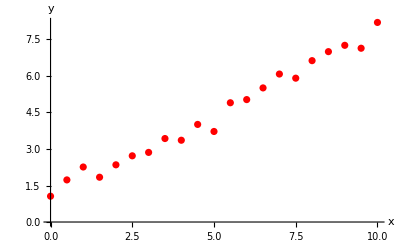

```mathematica
dataplot=ListPlot[data,AxesLabel->{x,y},PlotStyle->Red]
```

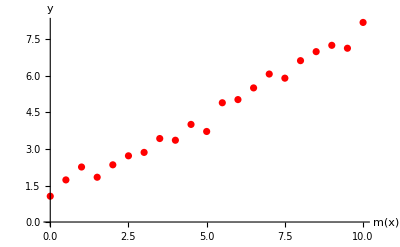

```mathematica
dataplot=ListPlot[data,AxesLabel->{m[x],y},PlotStyle->Red,Ticks->None,BaseStyle->{FontSize->12}]
```

We can now fit a straight line to the data using the method of least squares.

```mathematica
solution=FindFit[data,a x+b,{a,b},x]
```

{a→0.678416,b→1.03649}

```mathematica
y[x_]=a x+b/.solution
```

1.03649+0.678416 x

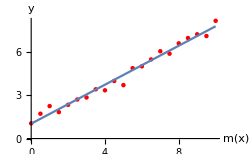

```mathematica
modelplot=Plot[y[x],{x,0,10},AxesLabel->{x,y}];
Show[dataplot,modelplot,ImageSize->250]
```

We can see that our model can be used for prediction, for example y(15).

```mathematica
y[15]
```

11.2127

The error that the prediction has depends on the distribution of data and number of measuring points. You’ll learn more about this in mathematical statistics.

That you can fit a straight line visually is a strong indication of a stable model.

#### 2.3.2 Exponential Function

The straight line can be used even if the model is not linear. As you might know the exponential gives a straight line in a semi-log plot (lin-log plot) in which the x-axis is linear and the y-axis is logarithmic. The scale on the y-axis is chosen using the inverse function y=e^x⇔ln(y)=x.

y=c e^(a x)⇔ln(y)=ln(c)+k x⇔ln(y)=a x+b⇔y=e^(a x+b)

y=c 10^(k x)⇔log_10(y)=log_10(c)+a x⇔log_10(y)=a x+b⇔y=10^(a x+b)

In other words, if we compute the logarithm of y-data we get a straight line.

Example:

```mathematica
ClearAll["`*"]
```

```mathematica
𝕩={0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.};
𝕪={2.88,5.65,9.61,6.32,10.5,15.2,17.5,30.9,28.8,55.1,41.1,134.,152.,248.,437.,368.,759.,1090.,1430.,1260.,3660.};
```

```mathematica
data=Transpose[{𝕩,𝕪}]
```

{{0.,2.88},{0.5,5.65},{1.,9.61},{1.5,6.32},{2.,10.5},{2.5,15.2},{3.,17.5},{3.5,30.9},{4.,28.8},{4.5,55.1},{5.,41.1},{5.5,134.},{6.,152.},{6.5,248.},{7.,437.},{7.5,368.},{8.,759.},{8.5,1090.},{9.,1430.},{9.5,1260.},{10.,3660.}}

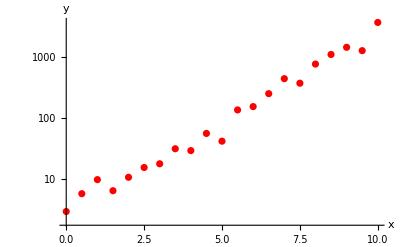

```mathematica
dataplot=ListLogPlot[data,AxesLabel->{x,y},PlotStyle->Red]
```

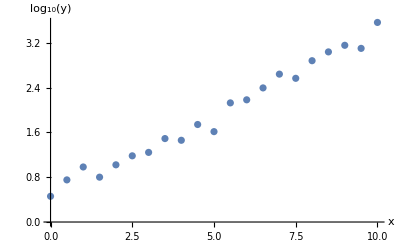

```mathematica
ListPlot[Transpose[{𝕩,Log10[𝕪]}],AxesLabel->{HoldForm[x],HoldForm[Log10[y]]}]
```

If data fits a straight line in a log(y)-lin(x) plot, then the model is an exponential.

```mathematica
data2=Transpose[{𝕩,Log[𝕪]}]
```

{{0.,1.05779},{0.5,1.73166},{1.,2.2628},{1.5,1.84372},{2.,2.35138},{2.5,2.7213},{3.,2.8622},{3.5,3.43076},{4.,3.36038},{4.5,4.00915},{5.,3.71601},{5.5,4.89784},{6.,5.02388},{6.5,5.51343},{7.,6.07993},{7.5,5.90808},{8.,6.632},{8.5,6.99393},{9.,7.26543},{9.5,7.13887},{10.,8.20522}}

```mathematica
solution=FindFit[data2,a x+b,{a,b},x]
```

{a→0.678348,b→1.0371}

```mathematica
y[x_]=ⅇ^(a x+b)/.solution
```

ⅇ^(1.0371+0.678348 x)

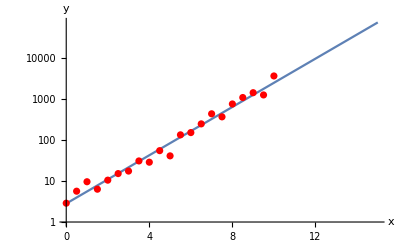

```mathematica
modelplot=LogPlot[y[x],{x,0,15},AxesLabel->{x,y}];
Show[modelplot,dataplot]
```

We can see that our model can be used for prediction, for example y(15).

```mathematica
y[15]
```

74037.4

Note: an exponential function a^x (Swe: exponentialfunktion) is a function where the exponential is the independent variable.

The other way around: Assume that our model ⅇ^(c y+d)=x is the model in focus.

ⅇ^(c y+d)=x⇔c y+d=ln(x)⇔y=1/c ln(x)-d/c⇔y=a ln(x)+b

In other words, if we compute the logarithm of x-data we get a straight line.

```mathematica
ClearAll["`*"]
```

```mathematica
𝕩={2.88,5.65,9.61,6.32,10.5,15.2,17.5,30.9,28.8,55.1,41.1,134.,152.,248.,437.,368.,759.,1090.,1430.,1260.,3660.};
𝕪={0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.};
```

```mathematica
data=Transpose[{𝕩,𝕪}]
```

{{2.88,0.},{5.65,0.5},{9.61,1.},{6.32,1.5},{10.5,2.},{15.2,2.5},{17.5,3.},{30.9,3.5},{28.8,4.},{55.1,4.5},{41.1,5.},{134.,5.5},{152.,6.},{248.,6.5},{437.,7.},{368.,7.5},{759.,8.},{1090.,8.5},{1430.,9.},{1260.,9.5},{3660.,10.}}

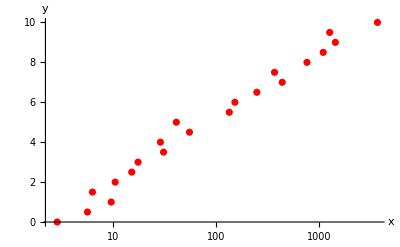

```mathematica
dataplot=ListLogLinearPlot[data,AxesLabel->{x,y},PlotStyle->Red]
```

If data fits a straight line in a lin(y)-log(x) plot, then the model is an logarithmic function.

```mathematica
data2=Transpose[{Log[𝕩],𝕪}]
```

{{1.05779,0.},{1.73166,0.5},{2.2628,1.},{1.84372,1.5},{2.35138,2.},{2.7213,2.5},{2.8622,3.},{3.43076,3.5},{3.36038,4.},{4.00915,4.5},{3.71601,5.},{4.89784,5.5},{5.02388,6.},{5.51343,6.5},{6.07993,7.},{5.90808,7.5},{6.632,8.},{6.99393,8.5},{7.26543,9.},{7.13887,9.5},{8.20522,10.}}

```mathematica
solution=FindFit[data2,a lnx+b,{a,b},lnx]
```

{a→1.44655,b→-1.40656}

```mathematica
y[x_]=a Log[x]+b/.solution
```

-1.40656+1.44655 Log[x]

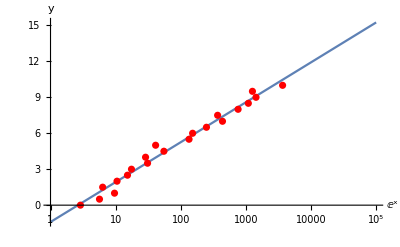

```mathematica
modelplot=LogLinearPlot[y[x],{x,1,10^5},AxesLabel->{x,y}];
Show[modelplot,dataplot]
```

We can see that our model can be used for prediction, for example y(10^5).

```mathematica
y[10^5]
```

15.2475

#### 2.3.3 Power Function

Now, assume our model is y=c x^a.

y=c x^a⇔ln(y)=ln(c)+a ln(x)⇔ln(y)=a ln(x)+b⇔y=e^b x^a

That is, if data compute the logarithm for both x and y we get a straight line.

Example:

```mathematica
ClearAll["`*"]
```

```mathematica
𝕩={1.,1.6,2.7,4.5,7.4,12.,20.,33.,55.,90.,150.,245.,400.,650.,1100.,1800.,3000.,5000.,8000.,13000.,22000.};
𝕪={2.88,5.65,9.61,6.32,10.5,15.2,17.5,30.9,28.8,55.1,41.1,134.,152.,248.,437.,368.,759.,1090.,1430.,1260.,3660.};
```

```mathematica
data=Transpose[{𝕩,𝕪}]
```

{{1.,2.88},{1.6,5.65},{2.7,9.61},{4.5,6.32},{7.4,10.5},{12.,15.2},{20.,17.5},{33.,30.9},{55.,28.8},{90.,55.1},{150.,41.1},{245.,134.},{400.,152.},{650.,248.},{1100.,437.},{1800.,368.},{3000.,759.},{5000.,1090.},{8000.,1430.},{13000.,1260.},{22000.,3660.}}

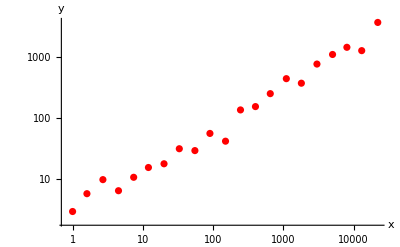

```mathematica
dataplot=ListLogLogPlot[data,AxesLabel->{x,y},PlotStyle->Red]
```

If data fits a straight line in a log(y)-log(x) plot, then the model is a power function.

```mathematica
data2=Transpose[{Log[𝕩],Log[𝕪]}]
```

{{0.,1.05779},{0.470004,1.73166},{0.993252,2.2628},{1.50408,1.84372},{2.00148,2.35138},{2.48491,2.7213},{2.99573,2.8622},{3.49651,3.43076},{4.00733,3.36038},{4.49981,4.00915},{5.01064,3.71601},{5.50126,4.89784},{5.99146,5.02388},{6.47697,5.51343},{7.00307,6.07993},{7.49554,5.90808},{8.00637,6.632},{8.51719,6.99393},{8.9872,7.26543},{9.4727,7.13887},{9.9988,8.20522}}

```mathematica
solution=FindFit[data2,a lnx+b,{a,b},lnx]
```

{a→0.678138,b→1.04092}

```mathematica
y[x_]=ⅇ^b x^a/.solution
```

2.83183 x^0.678138

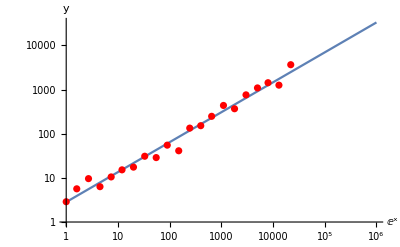

```mathematica
modelplot=LogLogPlot[y[x],{x,1,10^6},AxesLabel->{x,y}];
Show[modelplot,dataplot]
```

We can see that our model can be used for prediction, for example y(10^5).

```mathematica
y[10^6]
```

33181.4

Note: a power function x^a (Swe: potensfunktion) is a function where the base is the independent variable.

#### 2.3.4 General Function

We can use the idea of a straight line in a general function case. Let’s say we have a model function m(x) and we want to test this against data. Then we compute g(𝕩) and compare this with 𝕪. If we can fit a straight line we have a good model.

-Graphics-

Example:

```mathematica
ClearAll["`*"]
```

```mathematica
𝕩={0.,0.25,0.51,0.77,0.99,1.31,1.48,1.72,2.05,2.22,2.44,2.87,3.09,3.12,3.45,3.68,4.08,4.04,4.28,4.98,4.89};
𝕪={0.233,0.369,0.599,0.78,0.567,0.553,0.42,0.65,1.28,1.43,1.69,1.75,1.52,1.45,1.47,1.62,2.34,2.3,2.53,2.6,2.53};
```

```mathematica
data=Transpose[{𝕩,𝕪}];
```

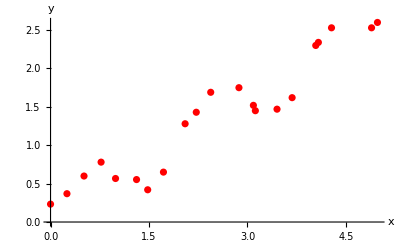

```mathematica
dataplot=ListPlot[data,AxesLabel->{x,y},PlotStyle->Red]
```

Assume that our model is y=m(x)=x/2 e^(-x/2)sin(π x)+x/2. We compute m(𝕩) and compare with given 𝕪. If this plot fits a straight line we have a good model function.

```mathematica
m[x_]:=x/2 ⅇ^(-x/2) Sin[π x]+x/2
```

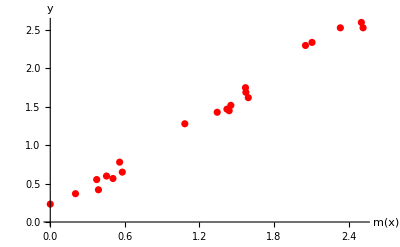

```mathematica
dataplotlin=ListPlot[Transpose[{m[𝕩],𝕪}],AxesLabel->{HoldForm[m[x]],HoldForm[y]},PlotStyle->Red]
```

Next, we compute the straight line parameters.

```mathematica
sol=FindFit[Transpose[{m[𝕩],𝕪}],a mx+b,{a,b},mx]
```

{a→0.989044,b→0.138891}

How is the line fit looking?

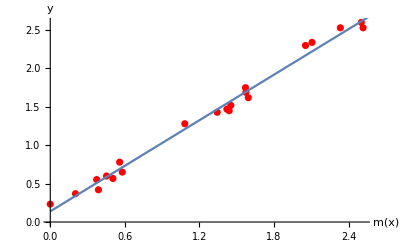

```mathematica
modelplotlin=Plot[a mx+b/.sol,{mx,0,4}];
Show[dataplotlin,modelplotlin]
```

The adjusted model is then:

```mathematica
f[x_]=Expand[a m[x]+b/.sol]
```

0.138891+0.494522 x+0.494522 ⅇ^(-x/2) x Sin[π x]

The model function and the original data:

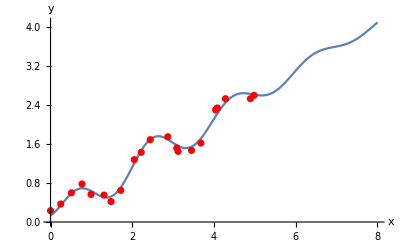

```mathematica
modelplot=Plot[f[x],{x,0,8},AxesLabel->{x,y}];
Show[modelplot,dataplot]
```

```mathematica
(* interpolation *)
f[3.85]
```

1.91671

```mathematica
(* predicition *)
f[8]
```

4.09507

## Section. Mathematical Task

Required for grade E (approved). Keep in mind that it is the mathematical method on the task that is interesting to consider, not the answer. Furthermore, solve the given task, not a variant or extension. A very good report and presentation is graded D.

Use KTH Canvas to discuss Mathematica code.

A general hint is to start in a small scale and test your methods with not too large numbers.

Take advantage of that you are using a mathematical programming language. Don’t “invent the wheel”. However, you are not supposed to use the built-in encryption methods, described in sections Section.Subsection.Subsubsection and Section.Subsection.Subsubsection.

```mathematica
ClearAll["`*"]
```

### RSA cipher

Professor Alice is sending a problem to the student Bob according to the procedure in section Section.Subsection.Subsubsection. You are supposed to solve Bob’s problem. However, you need to start by cracking the cipher sent to Bob. When translating to ASCII, you can assume the base 256.

```mathematica
nAlice=14625052655936968690439555839903578410656653152402266773966305647313;
eAlice=9103;
```

```mathematica
nBob=891257371165353198597686733461449215081540410212576138836198818353;
eBob=6389;
```

```mathematica
cipher={4430210573981968733755487447818174029880701596884938356564639003222,2851153559114750987221731555966122250132614620940651980091426872783,7706806242317911603638504323916964668918097951180075641184510131492,3684227409638269668959612918228029487936911649602484180495870360134,118390233898339944208891887229177617429671446231727377499079969939,11722755771961643408261179942790037153532726213028762901063706465880,13859812858423457720552211210177480158021647193707898449643563546715,8458200553283608142592103589289032864817455387331640007234518389001,4203062251335458332458951560795586742826858693125368654700629553235,11246017592897572378455633552556960091533916541949272900160606355164,528729157482321024630053104368111400799635858352035984875544277541,14149609332514930578966644135292557372570883055216115495760639164502,6806693065526086081574819023329054541636484663342321332752294055806,10173212145631688548727430811241580523813551542356631310237779750220,6759760040422316973322423168431166905944837651248859901210533615722,11488644301666039406597033276777701689096765993957684011886918061630,10421162414768710251337302689028405059375889881305351342596162625647,9496359638348947223087997149242581766202717301485526573539185466328,6021527813042783330194131859432644092333420618174656828129608651886,1862712526928231860818857411345402991522792361353775067366437910859,5770870235309404532139302393417410250573907045700501009827409811147,7754796273877044686482387739917927617087893337176831108280229804774,1689445149306311402232833597026076887079752228378923964144759423086,1448530945006829418385610770415140752515002298435493622427431846992,7445869507503892181715468267483205548161014207123217105479157092169,10975830923316626122520530596740793665823967057824410678091427215458,9807539864876132360289770201821020858873102738795986884424480971219};
```

The numbers is the list seems to be of the same size. Why?

Motivate your selected mathematical model!

```mathematica
{t1,f1}=AbsoluteTiming[FactorInteger[nBob]]
```

{789.621,{{457792861431456494922119050690577,1},{1946857293446017662241143108141089,1}}}

```mathematica
{{pBob,p},{qBob,q}} = f1
```

{{457792861431456494922119050690577,1},{1946857293446017662241143108141089,1}}

```mathematica
ϕBob=(pBob-1)(qBob-1)
```

891257371165353198597686733461446810431385532738418975574039986688

```mathematica
dBob=PowerMod[eBob,-1,ϕBob]
```

67796381653836540071760174121499945197942302224271657869617065821

```mathematica
dBob = 67796381653836540071760174121499945197942302224271657869617065821;
```

```mathematica
B=256;
```

```mathematica
For[i = 1, i < Length[cipher] +1, i++, 
cipher[[i]] = PowerMod[cipher[[i]],eAlice,nAlice]

]
```

```mathematica
For[i = 1, i < Length[cipher] +1, i++, 
cipher[[i]] = PowerMod[cipher[[i]], dBob, nBob]

]
```

```mathematica
For[i = 1, i < Length[cipher], i++, 
q=cipher[[i]];ascii={};
While[q≠0,
AppendTo[ascii,Mod[q,B]];
q=Quotient[q,B]
];
Print[FromCharacterCode[ascii]]
]
```

Congratulations! You have

now managed to crack the R

SA cipher. Your task is as

follows: write a method R

SAcrack[cipher,n,e] that w

ill crack a standard RSA c

ipher and delivers clear t

ext from the string cipher

. When you are finished wi

th your method, you should

investigate how long it w

ill take to crack the ciph

er of the Swedish text DIS

KRET MATTE, DE E FETT NAIS

! for different sizes on y

our public key n (100-200

bits). Visualize your resu

lts in a proper graph. It

is very important that you

study the section 2.3 in

the instructions. Your gra

ph should lead you to a mo

del where you can predict

how long it would take to

crack a cipher if n is 102

4, 2048 bits or 4096 bits

{52,44,32,50,48,52,56,32,98,105,116,115,32,111,114,32,52,48,57,54,32,98,105,116,115,32}

{112,104,32,115,104,111,117,108,100,32,108,101,97,100,32,121,111,117,32,116,111,32,97,32,109,111}

```mathematica
cip = 325230066098595166519846113430798858843;
nn = 2782761824826623128011717135735139377523;
ee = 6469;
RSAcrack[cip, nn, ee]
```

{0.17825,discrete math}

```mathematica
cPerson = 1505746645352771841845567883309719964315;
nPerson = 5412136652530931246239698616035133721479;
ePerson = 7769;
```

```mathematica
{time, message} = RSAcrack[cPerson,nPerson,ePerson]
```

{0.206817,discrete math}

```mathematica
time
message
```

0.203655

discrete math

```mathematica
(*message = "DISKRET";*)
message = "DISKRET MATTE, DE E FETT NAIS!";

splitText[message_, a_, b_]:= Module[{Bytes, ascii, F, B, i, eachLineBits, case},
eachLineBits = a +b;
Bytes = Floor[eachLineBits/8];
case = Bytes*8;
B = Which[case == eachLineBits, Bytes-1, True, Bytes];

ascii={};
(*Print[StringLength[message]];*)
For[i=1, i <StringLength[message]/B+1, i++, 
(*Print[StringTake[message,{(i-1)*B+1, i*B}]]*)
F =Which[i*B > StringLength[message], StringLength[message], True, i*B];
AppendTo[ascii, StringTake[message,{(i-1)*B +1, F}]]
]; 
ascii
]
(*a = splitText[save, 500,500]*)
(*a[[3]]*)

genCipher[message_, a_, b_] := 
Module[{ pPerson, qPerson, ϕPerson,ePerson, m, nPerson, c, i, rnd, ascii},
pPerson = NextPrime[RandomInteger[{2^a, 2^a}]];
qPerson = NextPrime[RandomInteger[{2^b, 2^b}]];
ϕPerson=(pPerson-1)(qPerson-1);
nPerson = pPerson*qPerson;
rnd:=RandomInteger[{10^3,10^4}];
While[GCD[ePerson=rnd,ϕPerson]≠1];

c = splitText[message, a, b];
For [i = 1, i < Length[c]+1, i++, 
c[[i]] = ToCharacterCode[c[[i]] ]. 256^(Range[StringLength[c[[i]]]]-1);

c[[i]] = PowerMod[c[[i]] , ePerson, nPerson];

];

(*{c, nPerson, ePerson, pPerson, qPerson}*)
{nPerson, ePerson,c}
]


(*Task 2*)
RSAcrack[cipher_, n_, e_] := 
Module[{t, f, pPerson, qPerson, ϕPerson, dPerson, mFromPerson, mInAscii, B, clearText, i, q, ascii,c},
{t, _G}=AbsoluteTiming[
{{pPerson,_V},{qPerson,_L}} = FactorInteger[n];
ϕPerson=(pPerson-1)(qPerson-1);
dPerson=PowerMod[e,-1,ϕPerson];
c =cipher;
For[i = 1, i <Length[cipher]+1, i++,
mFromPerson = PowerMod[cipher[[i]],dPerson,n];

q=mFromPerson;ascii={};

While[q≠0,
AppendTo[ascii,Mod[q,256]];
q=Quotient[q,256]
];
c[[i]] = FromCharacterCode[ascii];

];

];
clearText = StringJoin[c];
{t, clearText}
]


(*{n,e,c} = genCipher[save, 50, 52]
{t, m} = RSAcrack[c, n, e] *)
(*{t1,f1}=AbsoluteTiming[FactorInteger[n]]*)

genData[message_, amountData_, startBit1_, startBit2_] := Module[{n, e, c, data, t, s1, s2, i, sList, tList, sTotal},
data = {};
sList = {};
tList = {};
For[i=0, i < amountData+1, i++,
s1=startBit1 + i*2 ;
s2 = startBit2 +i*3;
sTotal = s1 + s2;
{n,e,c} = genCipher[message, s1 , s2 ];
{t, _m} = RSAcrack[c,n,e];
temp = {(s1+s2), t};
AppendTo[data,temp];
AppendTo[sList, sTotal];
AppendTo[tList, t];
];
{data, sList, tList}

]

{data, sList, tList} = genData[message, 20, 49,51]
```

{{{100,0.035166},{105,0.044213},{110,0.011726},{115,0.057296},{120,0.090224},{125,0.126629},{130,0.147893},{135,0.257551},{140,0.445158},{145,0.531661},{150,0.863216},{155,1.39832},{160,3.54705},{165,3.95085},{170,6.43355},{175,7.79738},{180,11.1327},{185,16.8007},{190,28.6981},{195,49.4828},{200,89.6505}},{100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200},{0.035166,0.044213,0.011726,0.057296,0.090224,0.126629,0.147893,0.257551,0.445158,0.531661,0.863216,1.39832,3.54705,3.95085,6.43355,7.79738,11.1327,16.8007,28.6981,49.4828,89.6505}}

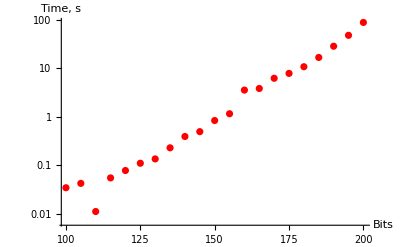

```mathematica
dataPlot = ListLogPlot[data, AxesLabel -> {"Bits", "Time, s"}, PlotStyle-> Red]
```

{a→0.083559,b→-12.4969}

ⅇ^(-12.4969+0.083559 x)

2.47823×10^61

1.63386×10^143

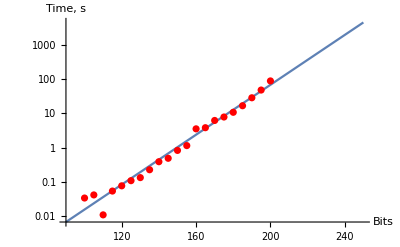

```mathematica
data2=Transpose[{sList,Log[tList]}];
solution=FindFit[data2,a x+b,{a,b},x]
y[x_]=ⅇ^(a x+b)/.solution
y[1024];
y[2048]/(60*60*24*365)
y[4096]
modelplot = LogPlot[y[x], {x,90,250}, AxesLabel -> {"Bits", "Time, s"}];
Show[modelplot, dataPlot]
```

```mathematica
7.815334181556091*^68
```

1.63386×10^143

-Graphics-

```mathematica
5.405222977657862*^31/(60*60*24*365)
```

1.71398×10^24